```mathematica
(* Import RHP library and set directory for files *)
AppendTo[$Path, " Your path to the RHPackage-master package here "];
<<RiemannHilbert`;
```

```mathematica
(* Set n - genus *)
n=1; 
ϕ={0.4,0.8};
```

```mathematica
nt=2^8 (* Number points in t domain *);
nλ=40;(* parameter p in GG *)
```

```mathematica
λ={0.2780+I,1.2780+I}
```

{0.278+1. ⅈ,1.278+1. ⅈ}

```mathematica
(* Riemann surface *)
w[z_]:=Product[√((z-Conjugate[λ[[i]]])/(z-λ[[i]]))(z-λ[[i]]), {i,n+1}] (* Why calculating this way? *);
```

```mathematica
K[ k_, j_]:= N[NIntegrate[(I(Re[λ[[j]]]+I x)^(k-1))/w[(Re[λ[[j]]]+I x-10^-10)],{x, -Im[λ[[j]]], Im[λ[[j]]]}]] (* 10^-10 to avoid singylarity? *);
```

```mathematica
(* Here the solving of linear equation system for Cf with Cf0=0 *)
If [n>1,Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-1], {-2Pi I}]]],Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-2Pi I}]]]
```

{0,3.11218+0. ⅈ}

```mathematica
(* Siganl period *)
Tnorm=Abs[2π/Min[Re[Cf[[2;;]]]]]
```

2.0189

```mathematica
(* Jump matrix *)
Clear[G];
G[_][_,_?InfinityQ]:=IdentityMatrix[2];
G[_][_,_?ZeroQ]:=IdentityMatrix[2];
Do[G[i][x_,z_]=({{0z, I Exp[-I(Cf[[i]] x)]Exp[-I ϕ[[i]]]}, {I Exp[I(Cf[[i]]x)]Exp[I ϕ[[i]]], 0z}})/.Underflow[]->0, {i, 1, n+1}];
```

```mathematica
(* Preparation Fun with G and main spectrum for Solver *)
GG[p_,x_]:=Table[Fun[G[j][x,#]&,Line[{Re[λ[[j]]]-I Im[λ[[j]]],Re[λ[[j]]]+I Im[λ[[j]]]}],p],{j,1,n+1}];
(* Points in t domain *)
trange=Range[-Tnorm/2, Tnorm/2, Tnorm/(nt-1)]+Tnorm/2 ;
Length[trange]
```

256

```mathematica
q1=0 trange;
For[ix=1,ix<=Length[trange],ix++,
U=RHSolve[GG[nλ,trange[[ix]]]];
q1[[ix]]=-1/π DomainIntegrate[U][[1,2]] ;
];
```

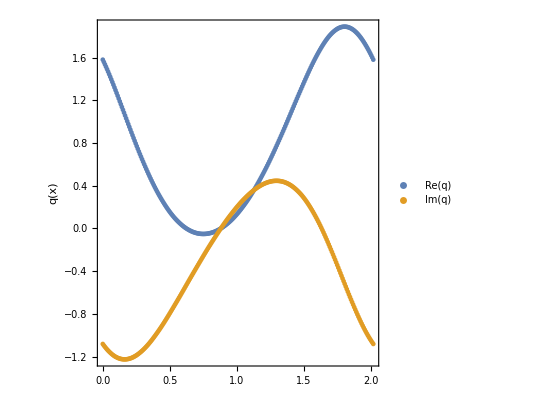

```mathematica
(* Signal plot *)
p1=ListPlot[{Transpose[{trange,Re[q1]}], Transpose[{trange,Im[q1]}]}, Frame->True, FrameStyle->Directive[Medium, Bold], PlotStyle->Bold,FrameLabel->{None,"q(x)"}, PlotLegends->Placed[{"Re(q)", "Im(q)"}, Above], AspectRatio->1,PlotRange->All]
```